# Frat. Hidráulico - Análise Conv.

## Parametros

```mathematica
μ=1 10^-8;(*(N/mm).s*)
elsize=50; (*mm*)
Q=100; (*mm3/s/mm*)
hf=50000;(*mm*)
Cl=0.3; (*esqueci*)
σc=20;(*N/mm2*)
Ela=1 10^4;(*N/mm2*)
ν=0.2;
G=Ela/(2(1+ν));
Δt=1;
```

## Abertura

```mathematica
w=(0.817(1-ν)hf)/G(pfrac-σc)
dwdp=(0.817(1-ν)hf)/G
```

7.8432 (-20+pfrac)

7.8432

## Leak-off

```mathematica
vlacum=1;
tfic=vlacum^2/(2 Cl)^2; (*Tempo ficticio*)
vlnext=2 Cl Sqrt[tfic+Δt];
Print["vlnext = ",vlnext];
qlanali=Cl/Sqrt[tfic+Δt];
ql=(vlnext-vlacum)/Δt;
dqldp=0;
Print["ql = ",ql];
```

vlnext = 1.16619

ql = 0.16619

## Variáveis

```mathematica
pini=20.0319;
qin=100;
qout=83.381;
wnum=w/.pfrac->pini
dwdpnum=dwdp/.pfrac->pini
cfg={pfrac->pini,Qin->qin,Qout->qout}
```

0.250198

7.8432

{pfrac→20.0319,Qin→100,Qout→83.381}

## Resíduo

Organizado com Lei Constitutiva primeiro (Q) e depois Conservação (p)

```mathematica
size=3;
Res=Table[0,{i,size}];
Res[[1]]=(12 μ)/w^3(Qin elsize/3+(Qout elsize)/6)-(-1/elsize)pfrac elsize;
Res[[2]]=(12 μ)/w^3(Qin elsize/6+(Qout elsize)/3)-(1/elsize)pfrac elsize+σc;
Res[[3]]=-((Qout-Qin)+1/Δt w elsize+2ql elsize);
1/Δt w elsize
Print["Res = ",Res/.cfg]
```

392.16 (-20+pfrac)

Res = {20.05,-0.0148677,-12.5099}

## Jacobiana

```mathematica
Jac=Table[0,{i,size},{j,size}];
(*iq x jq*)
Jac[[1,1]]=(12 μ)/w^3 elsize/3;
Jac[[1,2]]=(12 μ)/w^3 elsize/6;
Jac[[2,1]]=(12 μ)/w^3 elsize/6;
Jac[[2,2]]=(12 μ)/w^3 elsize/3;
(*iq x jp*)
Jac[[1,3]]=-3/w^4 dwdp 12μ (Qin elsize/3+(Qout elsize)/6)-(-1/elsize) elsize;
Jac[[2,3]]=-3/w^4 dwdp 12μ (Qin elsize/6+(Qout elsize)/3)-(1/elsize) elsize;
(*ip x jq*)
Jac[[3,1]]=-(-1/elsize)elsize;
Jac[[3,2]]=-(1/elsize)elsize;
(*ip x jp*)
Jac[[3,3]]=-(1/Δt dwdp +dqldp)elsize;

Print["Jac = ",Jac/.cfg//MatrixForm]
Jac/.cfg
```

Jac = (0.000127696 | 0.0000638481 | -0.701568
0.0000638481 | 0.000127696 | -2.60178
1 | -1 | -392.16)

{{0.000127696,0.0000638481,-0.701568},{0.0000638481,0.000127696,-2.60178},{1,-1,-392.16}}

-Graphics3D-

-Graphics3D-

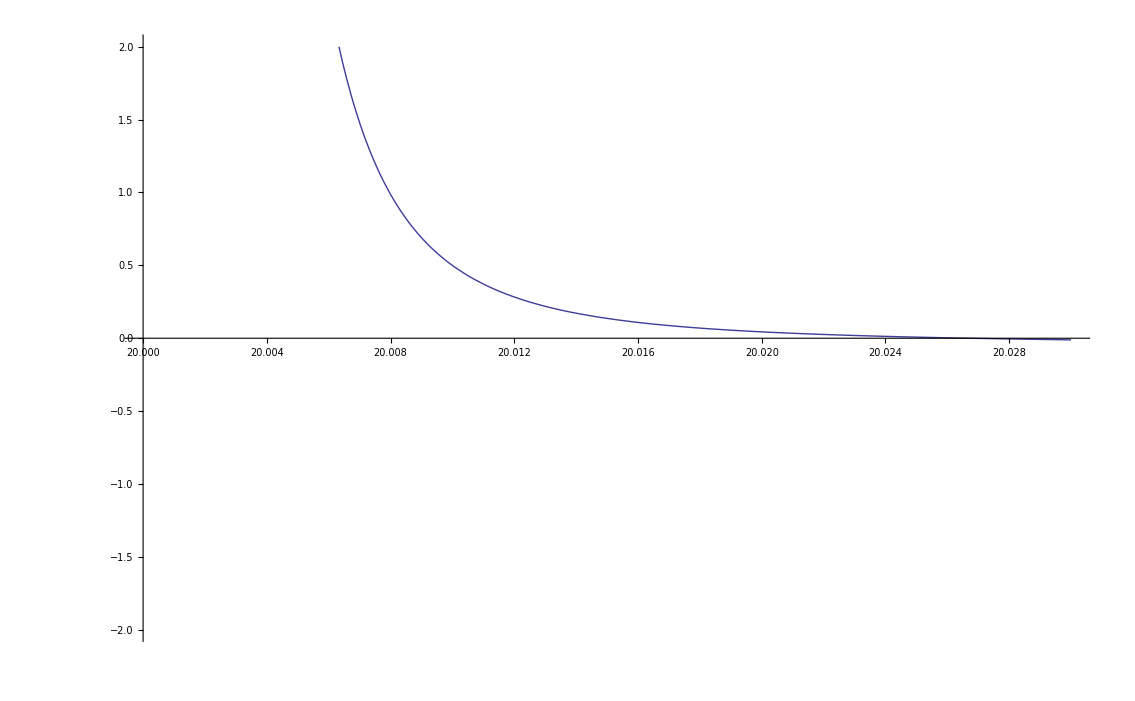

```mathematica
ResIn=Res/.Qin->100;
Plot3D[ResIn[[2]],{pfrac,20.000001,20.5},{Qout,35,50}]
Plot3D[ResIn[[3]],{pfrac,20.000001,21},{Qout,35,50}]
Plot[ResIn[[2]]/.Qout->72.9038,{pfrac,20.00001,20.03},PlotRange->{{20.00001,20.03},{-2,2}}]
```

```mathematica
0.33238075793811994 50
```

16.619

```mathematica
100-72.9038
```

27.0962